```mathematica
img  =-Graphics-
```

-Graphics-

```mathematica
gray=ImagePad[ImageCrop[ColorConvert[img,"Grayscale"],ImageDimensions[img]-6],10]
```

-Graphics-

```mathematica
bin=Binarize[gray,0.07]
```

-Graphics-

```mathematica
skeleton=Pruning[Pruning@Thinning[bin],15]
```

-Graphics-

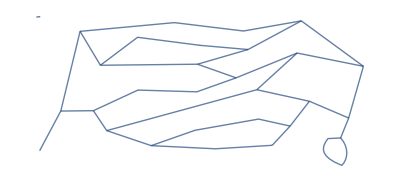

```mathematica
graph=MorphologicalGraph[skeleton]
```

```mathematica
EdgeRules[graph]
```

{1→2,3→5,3→9,3→13,4→5,4→6,6→12,6→20,7→8,7→12,8→9,9→11,10→13,10→14,10→15,11→12,11→14,13→21,14→17,15→18,15→25,16→17,16→19,18→21,18→23,19→20,19→25,20→30,21→26,22→23,22→24,23→27,24→28,25→28,26→26,27→29,28→29}

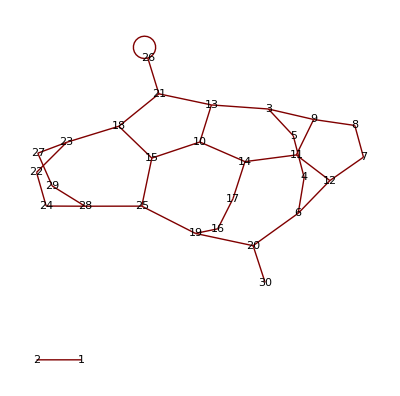

```mathematica
GraphPlot[EdgeRules[graph],VertexLabeling->True]
```

```mathematica
coordMapping=AssociationThread[VertexList[graph],GraphEmbedding[graph]]
```

<|1→{39.5,412.5},2→{29.5,411.5},3→{784.5,400.5},5→{619.5,371.5},9→{632.5,318.5},13→{961.5,270.5},4→{422.5,395.5},6→{153.5,370.5},12→{211.5,273.5},20→{98.5,142.5},7→{317.5,353.5},8→{495.5,330.5},11→{488.5,276.5},10→{772.5,308.5},14→{598.5,237.5},15→{657.5,203.5},21→{919.5,122.5},17→{486.5,197.5},18→{807.5,170.5},25→{229.5,86.5},16→{318.5,202.5},19→{191.5,143.5},23→{752.5,99.5},30→{38.5,29.5},26→{896.5,65.5},22→{662.5,119.5},24→{481.5,87.5},27→{701.5,44.5},28→{356.5,43.5},29→{539.5,34.5}|>

```mathematica
finalGraph=SimpleGraph@First@ConnectedGraphComponents[graph];
```

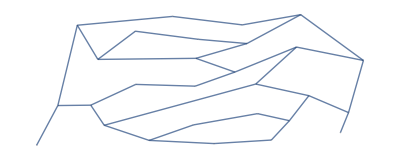

```mathematica
finalGraph=Graph[finalGraph,VertexCoordinates->Thread[VertexList[finalGraph]->Lookup[coordMapping,VertexList[finalGraph]]]]
```

```mathematica
indexGraph = IndexGraph[finalGraph]
```

-Graphics-

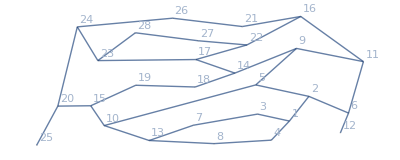

```mathematica
Show[SetProperty[indexGraph,VertexLabels->"Name"],PlotRange->All]
```

```mathematica
coordMapping=AssociationThread[VertexList[indexGraph],GraphEmbedding[indexGraph]]
```

<|1→{752.5,99.5},2→{807.5,170.5},3→{662.5,119.5},4→{701.5,44.5},5→{657.5,203.5},6→{919.5,122.5},7→{481.5,87.5},8→{539.5,34.5},9→{772.5,308.5},10→{229.5,86.5},11→{961.5,270.5},12→{896.5,65.5},13→{356.5,43.5},14→{598.5,237.5},15→{191.5,143.5},16→{784.5,400.5},17→{488.5,276.5},18→{486.5,197.5},19→{318.5,202.5},20→{98.5,142.5},21→{619.5,371.5},22→{632.5,318.5},23→{211.5,273.5},24→{153.5,370.5},25→{38.5,29.5},26→{422.5,395.5},27→{495.5,330.5},28→{317.5,353.5}|>

```mathematica
VertexCoordinates->Thread[VertexList[indexGraph]->Lookup[coordMapping,VertexList[indexGraph]]]
```

VertexCoordinates→{1→{752.5,99.5},2→{807.5,170.5},3→{662.5,119.5},4→{701.5,44.5},5→{657.5,203.5},6→{919.5,122.5},7→{481.5,87.5},8→{539.5,34.5},9→{772.5,308.5},10→{229.5,86.5},11→{961.5,270.5},12→{896.5,65.5},13→{356.5,43.5},14→{598.5,237.5},15→{191.5,143.5},16→{784.5,400.5},17→{488.5,276.5},18→{486.5,197.5},19→{318.5,202.5},20→{98.5,142.5},21→{619.5,371.5},22→{632.5,318.5},23→{211.5,273.5},24→{153.5,370.5},25→{38.5,29.5},26→{422.5,395.5},27→{495.5,330.5},28→{317.5,353.5}}

```mathematica
Show[img,Graph[finalGraph,GraphStyle->"ThickEdge",EdgeStyle->Opacity[0.6]],ImageSize->Full]
```

-Graphics-